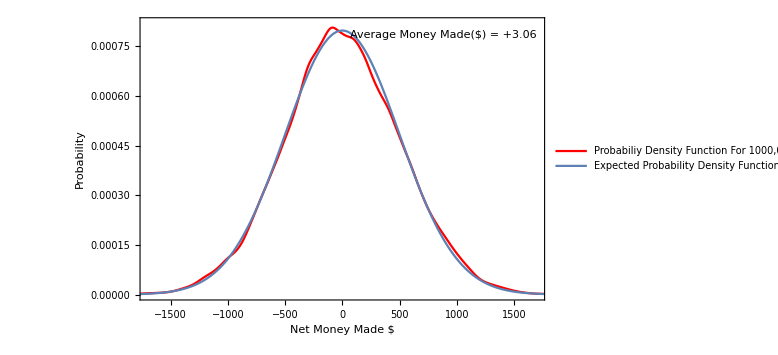

```mathematica
(* FAIR DYE WITH PROBABILITY OF WINNING = PROBABILITY OF LOSING *) 
(*----------------------------------------------------------------------------------------------------------------------------------------------*)

(* VARIABLES *) 
numberOfTrials = 0; (* total number of trials of the same *) 
probability = 1; (*initial value of probability *) 
scorePerThrow = 50; (* this defines the number of levels we have*) 
results = List[];
iterator = 0;  (* outer loop for total number of games *)
innerIter = 0; (* inner loop for total number of trials in one game *) 

(*CONSTANTS *) 
origBaseScore = 40000; 
lowerScore = 20000;
upperScore = 80000; 
targetScore = 42000; 
origLowerScore = lowerScore;
origUpperScore = upperScore; 
countInner = 100; 
countOuter = 10000;
runningScore = origBaseScore; 

While [iterator < countOuter , (*TOTAL NUMBER OF GAMES *) 

While [ innerIter < countInner , (* TOTAL NUMBER OF TRAILS PER GAME *) 
			myRandom = RandomInteger[5];
			If [ myRandom == 0  ∨myRandom == 1 ∨myRandom == 2 ,(* equal probability of increasing or decreasing score *) 
				runningScore = runningScore + scorePerThrow,
				runningScore  = runningScore - scorePerThrow
			   ];
	If[runningScore ≥  origUpperScore ∨  runningScore ≤  origLowerScore,(* IF WE CROSS THE SCORE BOUNDS,STOP ITERATIONS AND RESET *) 
	(*runningScore = 0;*)
	Break[]
	];

	innerIter++;	
	];
If [ runningScore ≠ 0,
	AppendTo[results, (runningScore-origBaseScore)];(* we save the net score *) 
];
runningScore = origBaseScore;
innerIter = 0; 
iterator++; 
	];

results;

(*CALCULATE AXIOMATIC PROBABILITY USING BINOMIAL DISTRIBUTION *) 


number = 10000; 
endLocation = 0;
expectedData = List[]; 

probabilityEquation = (number!)/(((number+endLocation)/2)!*((number-endLocation)/2)!)* ( 0.5)^((number+endLocation)/2)*( 0.5)^((number-endLocation)/2);

iterator = 0; 
DiscretePlot[Evaluate@Table[PDF[BinomialDistribution[1000,p],k],{p,{0.5}}],{k,800},PlotRange->All,PlotMarkers->Automatic];

expectedData = List[]; 
iterator = 0;
endLocation = -6000;
number = 10000; 
(* finding the probability of the score falling in these regions *) 
While [endLocation < 6000,
		endLocation = endLocation +scorePerThrow/10;
			
		probabilityValue = (number!)/(((number+endLocation)/2)!*((number-endLocation)/2)!)* ( 0.5)^((number+endLocation)/2)*( 0.5)^((number-endLocation)/2)/10;
		AppendTo[expectedData, {endLocation*5,probabilityValue}];
		iterator++;
	]
expectedData;
p2 = ListPlot[expectedData, PlotRange->All, Joined -> True,LabelStyle->{FontSize->14, Directive[Bold,Black]}, PlotLegends-> {"Expected Probability Density Function\n Using Binomial Distribution"}];

dataHistogram = SmoothHistogram[results, GridLines-> { {Mean[results]}}, GridLinesStyle-> Dashed,PlotRange->All,ImageSize->Large,Frame->True,FrameLabel->{"Net Money Made $","Probability",(*"Conditions= 
Starting Money = $40000; 
Money gained per each correct throw = $50;
FAIR dye i.e. P(WIN) = 3/6, P(LOSS) = 3/6
",""*)}, Epilog->Inset[Framed[Grid[{{"Average Money Made($) = "+Mean[results] //N}},Alignment->{{Left}}],Background->White],{1700,0.0008},{Right,Top}] ,  PlotLegends->{"Probabiliy Density  Function\n For 1000,000 Trials"},LabelStyle->{FontSize->14, Directive[Bold,Black]}, PlotStyle->{RGBColor[1,0,0],PointSize[0.005]}];
p2;
Show[{dataHistogram,p2} , PlotRange -> {{-1700,1700},{0,0.00082}}]

(* END  DYE *) 
(*----------------------------------------------------------------------------------------------------------------------------------------------*)
```

```mathematica
(* NEXT TWO PLOTS ARE THE SAME AS THIS ONE BUT THE DIES ARE NOT FAIR *)
```

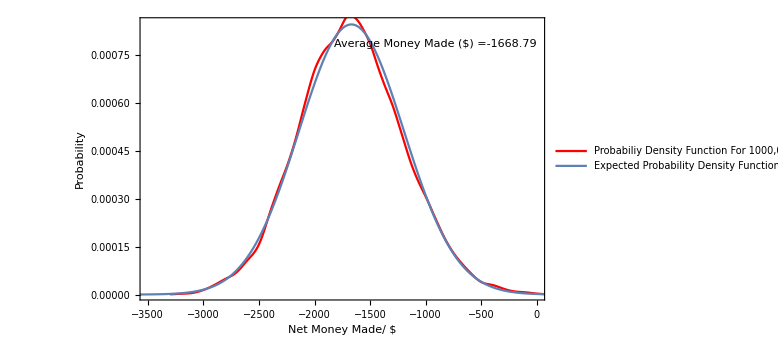

```mathematica
(*----------------------------------------------------------------------------------------------------------------------------------------------*)

(* UNFAIR DYE WITH PROBABILITY OF WINNING = 2/6 and PROBABILITY OF LOSING = 4/6*) 

numberOfTrials = 0; 
probability = 1;
scorePerThrow = 50; (* this defines the number of levels we have*) 
results = List[];
iterator = 0; 
innerIter = 0; 
origBaseScore = 40000; 
lowerScore = 20000;
upperScore = 80000; 
targetScore = 42000; 
origLowerScore = lowerScore;
origUpperScore = upperScore; 
countInner = 100; 
countOuter = 10000;
runningScore = origBaseScore; 

While [iterator < countOuter , 

While [ innerIter < countInner ,
			myRandom = RandomInteger[5];
			If [ myRandom == 0  ∨myRandom == 1 ,(* equal probability of increasing or decreasing score *) 
				runningScore = runningScore + scorePerThrow,
				runningScore  = runningScore - scorePerThrow
			   ];
	If[runningScore ≥  origUpperScore ∨  runningScore ≤  origLowerScore,
	(*runningScore = 0;*)
	Break[]
	];

	innerIter++;	
	];
If [ runningScore ≠ 0,
	AppendTo[results, (runningScore-origBaseScore)];
];
runningScore = origBaseScore;
innerIter = 0; 
iterator++; 
	];

results;
number = 10000; 
endLocation = -3000;
expectedData = List[]; 

probabilityEquation = (number!)/(((number+endLocation)/2)!*((number-endLocation)/2)!)* ( 2/6)^((number+endLocation)/2)*( 4/6)^((number-endLocation)/2)//N;

iterator = 0; 
DiscretePlot[Evaluate@Table[PDF[BinomialDistribution[1000,p],k],{p,{0.5}}],{k,800},PlotRange->All,PlotMarkers->Automatic];

expectedData = List[]; 
iterator = 0;
endLocation = -5000;
number = 10000;
While [endLocation < 0,
		endLocation = endLocation +scorePerThrow/10;
			
		probabilityValue = (number!)/(((number+endLocation)/2)!*((number-endLocation)/2)!)* ( 2/6)^((number+endLocation)/2)*( 4/6)^((number-endLocation)/2)/10;
		AppendTo[expectedData, {(endLocation*5)+15000,probabilityValue}];
		iterator++;
	]
expectedData;
p2 = ListPlot[expectedData, PlotRange->All, Joined -> True,LabelStyle->{FontSize->14, Directive[Bold,Black]}, PlotLegends-> {"Expected Probability Density Function \n Using Binomial Distribution"}];
dataHistogram = SmoothHistogram[results, GridLines-> { {Mean[results]}}, GridLinesStyle-> Dashed, PlotRange->All,ImageSize->Large,Frame->True,FrameLabel->{"Net Money Made/ $","Probability"(*,"Conditions= 
Starting Money = $40000;  
Money gained per each correct throw = $50;
UNFAIR dye i.e. P(WIN) = 2/6, P(LOSS) = 4/6
",""*)},Epilog->Inset[Framed[Grid[{{"Average Money Made ($) ="+Mean[results] //N}},Alignment->{{Left}}],Background->White],{0,0.0008},{Right,Top}] ,LabelStyle->{FontSize->14, Directive[Bold,Black]},  PlotLegends->{"Probabiliy Density Function \n For 1000,000 Trials"},PlotStyle->{RGBColor[1,0,0],PointSize[0.005]}];
p2;
Show[{dataHistogram,p2} , PlotRange -> {{-3500,0},{0,0.00085}}]
(* END  DYE *) 
(*----------------------------------------------------------------------------------------------------------------------------------------------*)
```

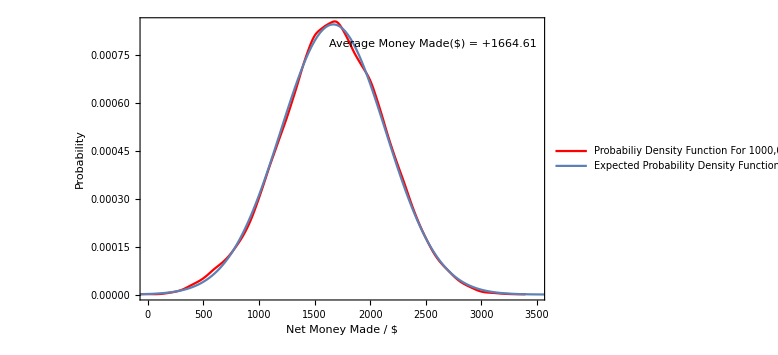

```mathematica
(*----------------------------------------------------------------------------------------------------------------------------------------------*)
(* UNFAIR DYE WITH PROBABILITY OF WINNING = 4/6 Probability of Losing = 2/6*) 
numberOfTrials = 0; 
probability = 1;
scorePerThrow = 50; (* this defines the number of levels we have*) 
results = List[];
iterator = 0; 
innerIter = 0; 
origBaseScore = 40000; 
lowerScore = 20000;
upperScore = 80000; 
targetScore = 42000; 
origLowerScore = lowerScore;
origUpperScore = upperScore; 
countInner = 100; 
countOuter = 10000;
runningScore = origBaseScore; 

While [iterator < countOuter , 

While [ innerIter < countInner ,
			myRandom = RandomInteger[5];
			If [ myRandom == 0  ∨myRandom == 1 ∨ myRandom == 2 ∨ myRandom == 3  ,(* equal probability of increasing or decreasing score *) 
				runningScore = runningScore + scorePerThrow,
				runningScore  = runningScore - scorePerThrow
			   ];
	If[runningScore ≥  origUpperScore ∨  runningScore ≤  origLowerScore,
	(*runningScore = 0;*)
	Break[]
	];

	innerIter++;	
	];
If [ runningScore ≠ 0,
	AppendTo[results, (runningScore-origBaseScore)];
];
runningScore = origBaseScore;
innerIter = 0; 
iterator++; 
	];

results;
number = 10000; 
endLocation = -3000;
expectedData = List[]; 

probabilityEquation = (number!)/(((number+endLocation)/2)!*((number-endLocation)/2)!)* ( 4/6)^((number+endLocation)/2)*( 2/6)^((number-endLocation)/2)//N;

iterator = 0; 
DiscretePlot[Evaluate@Table[PDF[BinomialDistribution[1000,p],k],{p,{0.5}}],{k,800},PlotRange->All,PlotMarkers->Automatic];

expectedData = List[]; 
iterator = 0;
endLocation = -1000;
number = 10000;
While [endLocation < 5000,
		endLocation = endLocation +scorePerThrow/10;
			
		probabilityValue = (number!)/(((number+endLocation)/2)!*((number-endLocation)/2)!)* ( 4/6)^((number+endLocation)/2)*( 2/6)^((number-endLocation)/2)/10;
		AppendTo[expectedData, {(endLocation*5)-15000,probabilityValue}];
		iterator++;
	]
expectedData;
p2 = ListPlot[expectedData, PlotRange->All, Joined -> True, LabelStyle->{FontSize->14, Directive[Bold,Black]}, PlotLegends-> {"Expected Probability Density Function \n Using Binomial Distribution"}];

dataHistogram = SmoothHistogram[results,PlotLegends->{"Probabiliy Density Function \n For 1000,000 Trials"},PlotRange->All,ImageSize->Large,Frame->True,GridLines-> { {Mean[results]}}, GridLinesStyle-> Dashed, FrameLabel->{"Net Money Made / $","Probability"(*,"Conditions= 
Starting Money = $40000;  
Money gained per each correct throw = $50;
UNFAIR dye i.e. P(WIN) = 4/6, P(LOSS) = 2/6
",""*)},LabelStyle->{FontSize->14, Directive[Bold,Black]}, PlotStyle->{RGBColor[1,0,0],PointSize[0.005]}, Epilog->Inset[Framed[Grid[{{"Average Money Made($) = "+ Mean[results] //N}},Alignment->{{Left}}],Background->White],{3500,0.0008},{Right,Top}] ];
p2;
Show[{dataHistogram,p2} , PlotRange -> {{0,3500},{0,0.00085}}]
```